## Common

```mathematica
AddMargin[g_]:=Framed[g,FrameStyle->None]
```

```mathematica
axesXYZ=Graphics[{
{Black,Thick,Arrowheads[0.25],Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}]},
{EdgeForm[{Black,Thick}],FaceForm[White],Disk[{0,0},0.12]},
{Black,Thick,Line[0.12*{{-1/√2,-1/√2},{1/√2,1/√2}}],Line[0.12*{{-1/√2,1/√2},{1/√2,-1/√2}}]},
{
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.85,0.25}],
Text[Style["ŷ",SingleLetterItalics->False,FontSize->25,FontFamily->"CMU Serif"],{0.25,0.25}],
Text[Style["ẑ",SingleLetterItalics->False,FontSize->25,FontFamily->"CMU Serif"],{0.25,0.85}]
}
},ImageSize->100]
```

-Graphics-

```mathematica
axesXYZ2=Graphics[{
{Black,Thick,Arrowheads[0.25],Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}]},
{EdgeForm[{Black,Thick}],FaceForm[White],Disk[{0,0},0.12]},
{Black,PointSize[Large],Point[{0,0}]},
{
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.85,0.25}],
Text[Style["ẑ",SingleLetterItalics->False,FontSize->25,FontFamily->"CMU Serif"],{0.25,0.25}],
Text[Style["ŷ",SingleLetterItalics->False,FontSize->25,FontFamily->"CMU Serif"],{0.25,0.85}]
}
},ImageSize->100]
```

-Graphics-

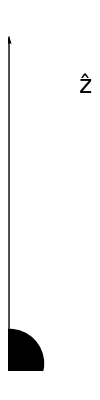

```mathematica
axesZ=Graphics[{
{Black,Thick,Arrowheads[1],Arrow[{{0,0},{0,1}}]},
{Black,PointSize->0.4,Point[{0,0}]},
Text[Style["ẑ",SingleLetterItalics->False,FontSize->25,FontFamily->"CMU Serif"],{0.25,0.85}]
},ImageSize->{Automatic,100}]
```

## class sphere

```mathematica
sphere=Graphics3D[{
{Black,PointSize[0.05],Point[{0,0,0}]},
{Opacity[0.7],Specularity[0.7],Cyan,Sphere[{0,1,0},0.5]},
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,0},{0.5,0,0}}]},
{Red,Thick,Line[0.05*{{-1,0,-1},{1,0,1}}],Line[0.05*{{1,0,-1},{-1,0,1}}]},
{Text[Style["r",FontSize->23,FontFamily->"Courier"],{0.25,0,0.1}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{0,-1,0},{0,0,0}},ViewVertical->{0,0,1},ImageSize->150]//AddMargin
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"sphere.png",sphere,RasterSize->300];
```

## class kmer

```mathematica
kmer=Grid[{
{
Item[Style["k = 3",FontSize->23,FontFamily->"Courier"],Alignment->Top],
Graphics3D[{
{Black,Thick,Dashed,Line[{{0,0,-1.3},{0,0,1.3}}]},
{Black,PointSize[Large],Point[{{0,0,-0.7},{0,0,0},{0,0,0.7}}]},
{Opacity[0.7],Specularity[0.7],Cyan,Sphere[{0,1,-0.7},0.5],Sphere[{0,1,0},0.5],Sphere[{0,1,0.7},0.5]},
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,-0.7},{1/(2 √2),0,-1/(2 √2)-0.7}}]},
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{-0.1,0,-0.7},{-0.1,0,0}}]},
{Red,Thick,Line[0.05*{{-1,-1,-1},{1,-1,1}}],Line[0.05*{{1,0,-1},{-1,0,1}}]},
{Text[Style["r",FontSize->23,FontFamily->"Courier"],{0.25,0,-0.75}]},
{Text[Style["distance",FontSize->23,FontFamily->"Courier"],{0.45,0,-0.35}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
},
{
Item[axesZ,Alignment->Bottom],
SpanFromAbove
}
},Spacings->1]//AddMargin
```

k = 3 | -Graphics3D-
-Graphics- |

```mathematica
Export[NotebookDirectory[]<>"kmer.png",kmer,RasterSize->{Automatic,500}];
```

## class polysphere_banana

```mathematica
CreatePolysphereBanana[n_,sR_,aR_,aA_]:=Module[{points,arcPoints,anglePoints,gEntries},
points=aR*{Cos[#],0,Sin[#]}&/@Subdivide[π-aA/2,π+aA/2,n-1];
arcPoints=aR*{Cos[#],0,Sin[#]}&/@Subdivide[π-1.3*aA/2,π+1.3*aA/2,100];
anglePoints=0.45*aR*{Cos[#],0,Sin[#]}&/@Subdivide[π-aA/2,π+aA/2,30];

gEntries={
(* spheres *)
{Opacity[0.7],Specularity[0.7],Cyan,Sphere[(#+{0,1,0})&/@points,sR]},
{Black,Thick,Dashed,Line[arcPoints],Line[{{0,0,0},points[[1]]}]},
(* arc *)
{Black,PointSize[Large],Point[{0,0,0}]},
{Black,PointSize[Large],Point[#&/@points]},
{Black,Thick,Arrowheads[0.05],Arrow[{{0,0,0},points[[1]]}],Arrow[{{0,0,0},points[[-1]]}]},
(*angle *)
{Black,Thick,Line[anglePoints]}
};

{points,gEntries}
]

sR=0.9;
{points1,gEntries1}=CreatePolysphereBanana[5,sR,2.5,2];
{points2,gEntries2}=CreatePolysphereBanana[10,sR,2.5,4];

polysphereBanana=Grid[{
{
Item[Style["sphere_n = 5",FontSize->17,FontFamily->"Courier"],Alignment->Top],
(* Left banana *)
Graphics3D[{
gEntries1,
(* origin *)
{Red,Thick,Line[((points1[[1]]+points1[[-1]])/2+#+{0,-1,0})&/@(0.1*{{-1,0,-1},{1,0,1}})],Line[((points1[[1]]+points1[[-1]])/2+#+{0,-1,0})&/@(0.1*{{1,0,-1},{-1,0,1}})]},
(* arc labels *)
{Text[Style["arc_r",FontSize->23,FontFamily->"Courier"],{-0.2,0,1.6}]},
{Text[Style["arc_angle",FontSize->23,FontFamily->"Courier"],{0.25,0,-0.2}]},
(* sphere_r and label *)

{Black,Thick,Arrowheads[0.05],Arrow[{points1[[-1]],points1[[-1]]+{sR,0,0}}]},
{Text[Style["sphere_r",FontSize->23,FontFamily->"Courier"],{-1,0,-2.5}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-2,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}],
(* Right banana *)
Graphics3D[{
gEntries2,
{Red,Thick,Line[(#+{0,-1,0})&/@(0.12*{{-1,0,-1},{1,0,1}})],Line[(#+{0,-1,0})&/@(0.12*{{1,0,-1},{-1,0,1}})]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-2,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
},
{
Item[axesXYZ,Alignment->Bottom],
SpanFromAbove,
SpanFromAbove,
SpanFromAbove
}
},Spacings->2,Dividers->{3->Thick}]//AddMargin
```

sphere_n = 5 | -Graphics3D- | -Graphics3D- | 
-Graphics- |  |  |

```mathematica
Export[NotebookDirectory[]<>"polysphere_banana.png",polysphereBanana,RasterSize->{Automatic,500}];
```

## class polysphere_lollipop

```mathematica
polysphereLollipop=Grid[{
{
Item[Style["sphere_n = 3",FontSize->17,FontFamily->"Courier"],Alignment->Top],
Graphics3D[{
(* spheres *)
{Black,Thick,Dashed,Line[{{0,0,-0.6},{0,0,2.3}}]},
{Black,PointSize[Large],Point[{{0,0,0},{0,0,0.6},{0,0,1.5}}]},
{Opacity[0.7],Specularity[0.7],Cyan,Sphere[{0,1,0},0.5],Sphere[{0,1,0.6},0.5],Sphere[{0,1,1.5},0.7]},
(* stick_penetration and tip_penetration *)
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{0.15,0,0.1},{0.15,0,0.5}}],Arrowheads[{0.04,-0.04}],Arrow[{{0.15,0,0.8},{0.15,0,1.1}}]},
{Black,Dashed,Thick,Line[{{0,0,0.1},{0.6,0,0.1}}],Line[{{0,0,0.5},{0.6,0,0.5}}],Line[{{0,0,0.8},{0.6,0,0.8}}],Line[{{0,0,1.1},{0.6,0,1.1}}]},
{Text[Style["stick_penetration",FontSize->23,FontFamily->"Courier"],{1.4,0,0.3}]},
{Text[Style["tip_penetration",FontSize->23,FontFamily->"Courier"],{1.25,0,0.92}]},
(* stick_r and tip_r *)
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,0},{0.5,0,0}}],Arrow[{{0,0,1.5},{0.7,0,1.5}}]},
{Text[Style["stick_r",FontSize->23,FontFamily->"Courier"],{0.2,0,-0.2}]},
{Text[Style["tip_r",FontSize->23,FontFamily->"Courier"],{0.37,0,1.7}]},
(* origin *)
{Red,Thick,Line[({0,-1,0.85}+#)&/@(0.05*{{-1,0,-1},{1,0,1}})],Line[({0,0,0.85}+#)&/@(0.05*{{1,0,-1},{-1,0,1}})]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
},
{
Item[axesZ,Alignment->Bottom],
SpanFromAbove
}
},Spacings->1]//AddMargin
```

sphere_n = 3 | -Graphics3D-
-Graphics- |

```mathematica
Export[NotebookDirectory[]<>"polysphere_lollipop.png",polysphereLollipop,RasterSize->{Automatic,500}];
```

## class polysphere_wedge

```mathematica
polysphereWedge=Grid[{
{
Item[Style["sphere_n = 3",FontSize->17,FontFamily->"Courier"],Alignment->Top],
Graphics3D[{
(* spheres *)
{Black,Thick,Dashed,Line[{{0,0,-0.6},{0,0,2.4}}]},
{Black,PointSize[Large],Point[{{0,0,0},{0,0,0.7},{0,0,1.6}}]},
{Opacity[0.7],Specularity[0.7],Cyan,Sphere[{0,1,0},0.5],Sphere[{0,1,0.7},0.6],Sphere[{0,1,1.6},0.7]},
(* penetration *)
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{0.15,0,0.1},{0.15,0,0.5}}],Arrow[{{0.15,0,0.9},{0.15,0,1.3}}]},
{Black,Dashed,Thick,Line[{{0,0,0.1},{0.6,0,0.1}}],Line[{{0,0,0.5},{0.6,0,0.5}}],Line[{{0,0,0.9},{0.6,0,0.9}}],Line[{{0,0,1.3},{0.6,0,1.3}}]},
{Text[Style["penetration",FontSize->23,FontFamily->"Courier"],{1.0,0,0.3}]},
(* bottom_r and top_r *)
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,0},{0.5,0,0}}],Arrow[{{0,0,1.6},{0.7,0,1.6}}]},
{Text[Style["bottom_r",FontSize->23,FontFamily->"Courier"],{0.2,0,-0.2}]},
{Text[Style["top_r",FontSize->23,FontFamily->"Courier"],{0.35,0,1.75}]},
(* origin *)
{Red,Thick,Line[({0,-1,0.9}+#)&/@(0.05*{{-1,0,-1},{1,0,1}})],Line[({0,0,0.9}+#)&/@(0.05*{{1,0,-1},{-1,0,1}})]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
},
{
Item[axesZ,Alignment->Bottom],
SpanFromAbove
}
},Spacings->1]//AddMargin
```

sphere_n = 3 | -Graphics3D-
-Graphics- |

```mathematica
Export[NotebookDirectory[]<>"polysphere_wedge.png",polysphereWedge,RasterSize->{Automatic,500}];
```

## class spherocylinder

```mathematica
spherocylinder=Grid[{{
Item[axesZ,Alignment->Bottom],
Graphics3D[{
(* spherocylinder *)
{Black,PointSize[Large],Point[{{0,0,-1},{0,0,1}}]},
{Opacity[0.7],Specularity[0.7],Cyan,Tube[{{0,1,-1},{0,1,1}},0.5]},
(* origin *)
{Red,Thick,Line[0.05*{{-1,0,-1},{1,0,1}}],Line[0.05*{{1,0,-1},{-1,0,1}}]},
(* caps, r *)
{Black,Thick,Dashed,Line[{{0,0,-1.6},{0,0,1.6}}]},
{Black,Thick,Dashed,Line[{0.5Sin[#],0,-1+0.5Cos[#]}&/@Subdivide[0,2π,50]],Line[{0.5Sin[#],0,1+0.5Cos[#]}&/@Subdivide[0,2π,50]]},
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,-1},{0,0,-1}+{1/(2 √2),0,-1/(2 √2)}}]},
{Text[Style["r",FontSize->23,FontFamily->"Courier"],{0.25,0,-1.05}]},
(* l *)
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{0.1,0,-1},{0.1,0,1}}]},
{Text[Style["l",FontSize->23,FontFamily->"Courier"],{0.25,0,0}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
}},Spacings->1]//AddMargin
```

-Graphics- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"spherocylinder.png",spherocylinder,RasterSize->{Automatic,500}];
```

## class polyspherocylinder_banana

```mathematica
CreatePolyspherocylinderBanana[n_,sR_,aR_,aA_]:=Module[{points,arcPoints,anglePoints,DrawCircle,gEntries},
points=aR*{Cos[#],0,Sin[#]}&/@Subdivide[π-aA/2,π+aA/2,n];
arcPoints=aR*{Cos[#],0,Sin[#]}&/@Subdivide[π-1.3*aA/2,π+1.3*aA/2,100];
anglePoints=0.45*aR*{Cos[#],0,Sin[#]}&/@Subdivide[π-aA/2,π+aA/2,30];
DrawCircle[o_]:=Line[o+{sR Sin[#],0,sR Cos[#]}&/@Subdivide[0,2π,50]];

gEntries={
(* spherocylinders *)
{Opacity[0.7],Specularity[0.7],Cyan,Tube[(#+{0,1,0})&/@points,sR]},
{Black,Thick,Dashed,Line[arcPoints],Line[{{0,0,0},points[[1]]}]},
{Black,Thick,Dashed,DrawCircle[points[[1]]],DrawCircle[points[[-1]]]},
(* arc *)
{Black,PointSize[Large],Point[{0,0,0}]},
{Black,PointSize[Large],Point[#&/@points]},
{Black,Thick,Arrowheads[0.05],Arrow[{{0,0,0},points[[1]]}],Arrow[{{0,0,0},points[[-1]]}]},
(*angle *)
{Black,Thick,Line[anglePoints]}
};

{points,gEntries}
]

sR=0.9;
{points1,gEntries1}=CreatePolyspherocylinderBanana[3,sR,2.5,2];
{points2,gEntries2}=CreatePolyspherocylinderBanana[5,sR,2.5,4];

polyspherocylinderBanana=Grid[{
{
Item[Style["segment_n = 3",FontSize->17,FontFamily->"Courier"],Alignment->Top],
(* Left banana *)
Graphics3D[{
gEntries1,
(* origin *)
{Red,Thick,Line[((points1[[1]]+points1[[-1]])/2+#+{0,-1,0})&/@(0.1*{{-1,0,-1},{1,0,1}})],Line[((points1[[1]]+points1[[-1]])/2+#+{0,-1,0})&/@(0.1*{{1,0,-1},{-1,0,1}})]},
(* arc labels *)
{Text[Style["arc_r",FontSize->23,FontFamily->"Courier"],{-0.2,0,1.6}]},
{Text[Style["arc_angle",FontSize->23,FontFamily->"Courier"],{0.25,0,-0.2}]},
(* sphere_r and label *)

{Black,Thick,Arrowheads[0.05],Arrow[{points1[[-1]],points1[[-1]]+{sR,0,0}}]},
{Text[Style["sc_r",FontSize->23,FontFamily->"Courier"],{-1,0,-2.5}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-2,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}],
(* Right banana *)
Graphics3D[{
gEntries2,
{Red,Thick,Line[(#+{0,-1,0})&/@(0.12*{{-1,0,-1},{1,0,1}})],Line[(#+{0,-1,0})&/@(0.12*{{1,0,-1},{-1,0,1}})]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-2,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
},
{
Item[axesXYZ,Alignment->Bottom],
SpanFromAbove,
SpanFromAbove,
SpanFromAbove
}
},Spacings->2,Dividers->{3->Thick}]//AddMargin
```

segment_n = 3 | -Graphics3D- | -Graphics3D- | 
-Graphics- |  |  |

```mathematica
Export[NotebookDirectory[]<>"polyspherocylinder_banana.png",polyspherocylinderBanana,RasterSize->{Automatic,500}];
```

## class smooth_wedge

```mathematica
smoothWedgeComplex=Translate[ToExpression[Import[NotebookDirectory[]<>"smooth_wedge.nb","String"]][[2,1]],{0,1,0}];
smoothWedge=Grid[{{
Item[axesZ,Alignment->Bottom],
Graphics3D[{
(* wedge *)
{Opacity[0.7],Specularity[0.7],EdgeForm[None],Cyan,smoothWedgeComplex},
{Black,Thick,Dashed,Line[{{0,0,-1.7},{0,0,1.7}}]},
(* origin *)
{Red,Thick,Line[0.05*{{-1,0,-1},{1,0,1}}],Line[0.05*{{1,0,-1},{-1,0,1}}]},
(* caps *)
{Black,PointSize[Large],Point[{{0,0,-1.1},{0,0,0.9}}]},
{Black,Thick,Dashed,Line[{0.5Sin[#],0,-1.1+0.5Cos[#]}&/@Subdivide[0,2π,50]],Line[{0.7Sin[#],0,0.9+0.7Cos[#]}&/@Subdivide[0,2π,50]]},
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,-1.1},{0.5,0,-1.1}}]},
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,0.9},{0.7,0,0.9}}]},
{Text[Style["bottom_r",FontSize->23,FontFamily->"Courier"],{0.25,0,-1.3}]},
{Text[Style["top_r",FontSize->23,FontFamily->"Courier"],{0.35,0,1.1}]},
(* l *)
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{0.1,0,-1.1},{0.1,0,0.9}}]},
{Text[Style["l",FontSize->23,FontFamily->"Courier"],{0.25,0,0}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]
}},Spacings->1]//AddMargin
```

-Graphics- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"smooth_wedge.png",smoothWedge,RasterSize->{Automatic,500}];
```

## class polyhedral_wedge

```mathematica
bottomAx=0.5;
bottomAy=0.3;
topAx=0.4;
topAy=0.7;
length=1.5;

points={
{bottomAx/2,bottomAy/2,-length/2},{-bottomAx/2,bottomAy/2,-length/2},{-bottomAx/2,-bottomAy/2,-length/2},{bottomAx/2,-bottomAy/2,-length/2},
{topAx/2,topAy/2,length/2},{-topAx/2,topAy/2,length/2},{-topAx/2,-topAy/2,length/2},{topAx/2,-topAy/2,length/2}
};

coordinates=Graphics3D[{
{Darker[Gray],Thick,Arrowheads[0.2],Specularity[0.4],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]},
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.8,0.4,0}],
Text[Style["ŷ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0,1.2,0}],
Text[Style["ẑ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.2,0,0.9}]
},Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,1},{0,0,0}},ViewVertical->{0,0,1},ViewAngle->1.9,ImageSize->100];

theWedge=Graphics3D[{
(* wedge *)
{Opacity[0.5],Specularity[0.7],EdgeForm[Directive[Thickness[0.015],Black]],Cyan,ConvexHullMesh[points]},
{Black,PointSize[Large],Point[{{0,0,-length/2},{0,0,length/2}}]},
(* origin *)
{Red,Thick,Line[0.05*{{-1,0,-1},{1,0,1}}],Line[0.05*{{1,0,-1},{-1,0,1}}]},
(* l *)
{
Black,Thick,Dashed,
Line[{{0,0,-length/2-0.2},{0,0,length/2+0.2}}],
Line[{{0,0,-length/2},{0.6,0,-length/2}}],Line[{{0,0,length/2},{0.6,0,length/2}}]
},
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{0.5,0,-length/2},{0.5,0,length/2}}]},
{Text[Style["l",FontSize->23,FontFamily->"Courier"],{0.6,0,0}]},
(* bottom *)
{
Black,Thick,Dashed,
Line[{{-bottomAx/2,-bottomAy/2,-length/2},{-bottomAx/2,-bottomAy/2-0.3,-length/2}}],
Line[{{bottomAx/2,-bottomAy/2,-length/2},{bottomAx/2,-bottomAy/2-0.3,-length/2}}],
Line[{{-bottomAx/2-0.3,-bottomAy/2,-length/2},{-bottomAx/2,-bottomAy/2,-length/2}}],
Line[{{-bottomAx/2-0.3,bottomAy/2,-length/2},{-bottomAx/2,bottomAy/2,-length/2}}]
},
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{-bottomAx/2,-bottomAy/2-0.15,-length/2},{bottomAx/2,-bottomAy/2-0.15,-length/2}}]},
{Black,Thick,Arrowheads[{-0.03,0.03}],Arrow[{{-bottomAx/2-0.2,-bottomAy/2,-length/2},{-bottomAx/2-0.2,bottomAy/2,-length/2}}]},
{Text[Style["bottom_ax",FontSize->23,FontFamily->"Courier"],{-0.3,-0.6,-length/2}]},
{Text[Style["bottom_ay",FontSize->23,FontFamily->"Courier"],{-0.9,-0.1,-length/2}]},
(* top *)
{
Black,Thick,Dashed,
Line[{{-topAx/2,-topAy/2,length/2},{-topAx/2,-topAy/2-0.3,length/2}}],
Line[{{topAx/2,-topAy/2,length/2},{topAx/2,-topAy/2-0.3,length/2}}],
Line[{{-topAx/2-0.3,-topAy/2,length/2},{-topAx/2,-topAy/2,length/2}}],
Line[{{-topAx/2-0.3,topAy/2,length/2},{-topAx/2,topAy/2,length/2}}]
},
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{-topAx/2,-topAy/2-0.15,length/2},{topAx/2,-topAy/2-0.15,length/2}}]},
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{-topAx/2-0.2,-topAy/2,length/2},{-topAx/2-0.2,topAy/2,length/2}}]},
{Text[Style["top_ax",FontSize->23,FontFamily->"Courier"],{-0.25,-0.85,length/2}]},
{Text[Style["top_ay",FontSize->23,FontFamily->"Courier"],{-0.7,-0,length/2}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{1,-2,1},ViewVertical->{0,0,1},ImageSize->{Automatic,300}];

polyhedralWedge=Grid[{{Item[coordinates,Alignment->Bottom],theWedge}},Spacings->1]//AddMargin
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"polyhedral_wedge.png",polyhedralWedge,RasterSize->{Automatic,500}];
```

## class polysphere

```mathematica
polysphere=Graphics3D[{
{Specularity[0.2],Darker[Cyan],Sphere[{0,0,0},0.5],Sphere[0.7*{{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}},0.35]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1.5,1,0.5},{0,0,0}},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]//AddMargin
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"polysphere.png",polysphere,RasterSize->{Automatic,400}];
```

## class polyspherocylinder

```mathematica
polyspherocylinder=Graphics3D[{
{
Specularity[0.2],Darker[Cyan],
Tube[{{0,0,2},{0,0,-2}},1],Tube[{{1,-1,0},{1,1,0}},0.7],Tube[{{-1,-1,0},{1,-1,0}},0.7],Tube[{{-1,1,0},{-1,-1,0}},0.7],Tube[{{1,1,0},{-1,1,0}},0.7]
}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{3,2,1},{0,0,0}},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]//AddMargin
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"polyspherocylinder.png",polyspherocylinder,RasterSize->{Automatic,400}];
```

## class generic_convex

```mathematica
genericConvexComplex=ToExpression[Import[NotebookDirectory[]<>"generic_convex.nb","String"]][[2,1]];
genericConvex=Graphics3D[{{EdgeForm[None],Specularity[0.2],Darker[Cyan],genericConvex}},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{3,2,1},{0,0,0}},ViewVertical->{0,0,1},ImageSize->{Automatic,300}]//AddMargin
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"generic_convex.png",genericConvex,RasterSize->{Automatic,400}];
```

### point primitive

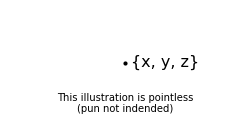

```mathematica
point=Graphics[{
{PointSize->Large,Point[{0,0}]},
{Text[Style["This illustration is pointless\n(pun not indended)",FontFamily->"Courier",FontSize->10],{0,-0.4}]},
Text[Style["{x, y, z}",FontFamily->"Courier",FontSize->16],{0.5,0}]
},ImageSize->250,PlotRange->{{-1,1},{-0.5,0.5}}]
```

```mathematica
Export[NotebookDirectory[]<>"point.png",point,RasterSize->{Automatic,250}];
```

### segment primitive

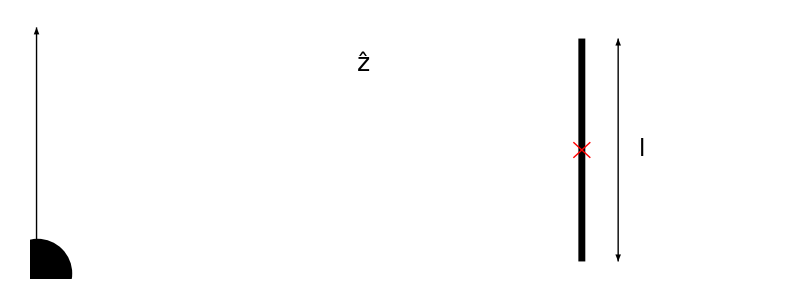

```mathematica
segment=Grid[{{
axesZ,Graphics[{
{Black,Thickness[0.025],CapForm["Round"],Line[{{0,-1},{0,1}}]},
{Black,Thick,Arrowheads[{-0.1,0.1}],Arrow[{{0.3,-1},{0.3,1}}]},
{Red,Thick,Line[0.07*{{-1,-1},{1,1}}],Line[0.07*{{1,-1},{-1,1}}]},
Text[Style["l",FontFamily->"Courier",FontSize->23],{0.5,0}]
},ImageSize->200,PlotRange->{{-1.2,1.5},{-1.1,1.1}}]
}},Spacings->0,Alignment->Bottom]//AddMargin
```

```mathematica
Export[NotebookDirectory[]<>"segment.png",segment,RasterSize->{Automatic,250}];
```

### rectangle primitive

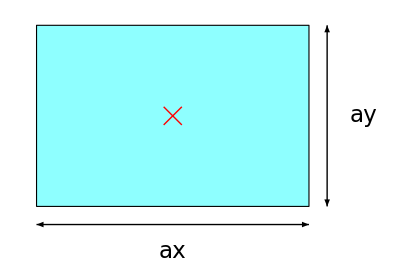
-Graphics- | -Graphics-

```mathematica
rectangle=Grid[{{
axesXYZ2,Graphics[{
{Black,EdgeForm[{Black,Thick}],FaceForm[Lighter@Lighter@Cyan],Rectangle[{-1.5,-1},{1.5,1}]},
{Black,Thick,Arrowheads[{-0.1,0.1}],Arrow[{{1.7,-1},{1.7,1}}],Arrow[{{-1.5,-1.2},{1.5,-1.2}}]},
{Red,Thick,Line[0.1*{{-1,-1},{1,1}}],Line[0.1*{{1,-1},{-1,1}}]},
Text[Style["ay",FontFamily->"Courier",FontSize->23],{2.1,0}],
Text[Style["ax",FontFamily->"Courier",FontSize->23],{0,-1.5}]
},ImageSize->{Automatic,140}]
}},Spacings->1,Alignment->Bottom]//AddMargin
```

```mathematica
Export[NotebookDirectory[]<>"rectangle.png",rectangle,RasterSize->{Automatic,250}];
```

### cuboid primitive

```mathematica
ax=0.7;
ay=1.0;
az=1.5;

coordinates=Graphics3D[{
{Darker[Gray],Thick,Arrowheads[0.2],Specularity[0.4],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]},
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.8,0.4,0}],
Text[Style["ŷ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0,1.2,0}],
Text[Style["ẑ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.2,0,0.9}]
},Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,1},{0,0,0}},ViewVertical->{0,0,1},ViewAngle->1.9,ImageSize->100];

theCuboid=Graphics3D[{
(* cuboid *)
{Opacity[0.5],Specularity[0.7],EdgeForm[Directive[Thickness[0.015],Black]],Cyan,Cuboid[{-ax/2,-ay/2,-az/2},{ax/2,ay/2,az/2}]},
{Black,PointSize[Large],Point[{{0,0,-az/2},{0,0,az/2}}]},
(* origin *)
{Red,Thick,Line[0.05*{{-1,0,-1},{1,0,1}}],Line[0.05*{{1,0,-1},{-1,0,1}}]},
(* l *)
{
Black,Thick,Dashed,
Line[{{0,0,-az/2-0.2},{0,0,az/2+0.2}}]
},
(* sides *)
{
Black,Thick,Dashed,
Line[{{-ax/2,-ay/2,-az/2},{-ax/2,-ay/2-0.3,-az/2}}],
Line[{{ax/2,-ay/2,-az/2},{ax/2,-ay/2-0.3,-az/2}}],
Line[{{ax/2,-ay/2,-az/2},{ax/2+0.3,-ay/2,-az/2}}],
Line[{{ax/2,ay/2,-az/2},{ax/2+0.3,ay/2,-az/2}}],
Line[{{ax/2,ay/2,az/2},{ax/2+0.3,ay/2,az/2}}]
},
{Black,Thick,Arrowheads[{-0.05,0.05}],Arrow[{{-ax/2,-ay/2-0.15,-az/2},{ax/2,-ay/2-0.15,-az/2}}]},
{Black,Thick,Arrowheads[{-0.05,0.05}],Arrow[{{ax/2+0.2,-ay/2,-az/2},{ax/2+0.2,ay/2,-az/2}}]},
{Black,Thick,Arrowheads[{-0.05,0.05}],Arrow[{{ax/2+0.2,ay/2,-az/2},{ax/2+0.2,ay/2,az/2}}]},
{Text[Style["ax",FontSize->23,FontFamily->"Courier"],{0.05,-0.9,-az/2}]},
{Text[Style["ay",FontSize->23,FontFamily->"Courier"],{0.75,-0.1,-az/2}]},
{Text[Style["az",FontSize->23,FontFamily->"Courier"],{0.75,0.5,0}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{1,-2,1},ViewVertical->{0,0,1},ImageSize->{Automatic,250}];

cuboid=Grid[{{coordinates,theCuboid}},Spacings->1,Alignment->Bottom]//AddMargin
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"cuboid.png",cuboid,RasterSize->{Automatic,400}];
```

### disk primitive

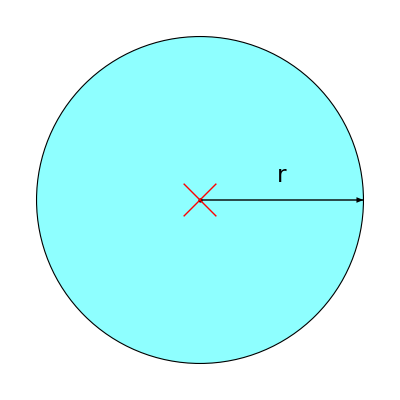
-Graphics- | -Graphics-

```mathematica
disk=Grid[{{
axesXYZ2,Graphics[{
{Black,EdgeForm[{Black,Thick}],FaceForm[Lighter@Lighter@Cyan],Disk[{0,0},1]},
{Black,PointSize[Large],Point[{0,0}]},
{Black,Thick,Arrowheads[0.1],Arrow[{{0,0},{1,0}}]},
{Red,Thick,Line[0.1*{{-1,-1},{1,1}}],Line[0.1*{{1,-1},{-1,1}}]},
Text[Style["r",FontFamily->"Courier",FontSize->23],{0.5,0.15}]
},ImageSize->{Automatic,140}]
}},Spacings->1,Alignment->Bottom]//AddMargin
```

```mathematica
Export[NotebookDirectory[]<>"disk.png",disk,RasterSize->{Automatic,250}];
```

### ellipse primitive

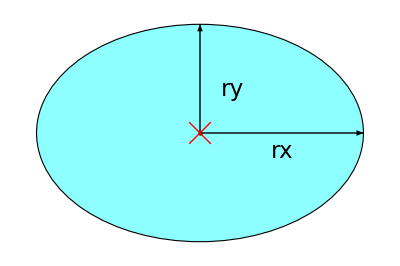
-Graphics- | -Graphics-

```mathematica
ellipse=Grid[{{
axesXYZ2,Graphics[{
{Black,EdgeForm[{Black,Thick}],FaceForm[Lighter@Lighter@Cyan],Disk[{0,0},{1.5,1}]},
{Black,PointSize[Large],Point[{0,0}]},
{Black,Thick,Arrowheads[0.1],Arrow[{{0,0},{1.5,0}}],Arrow[{{0,0},{0,1}}]},
{Red,Thick,Line[0.1*{{-1,-1},{1,1}}],Line[0.1*{{1,-1},{-1,1}}]},
Text[Style["rx",FontFamily->"Courier",FontSize->23],{0.75,-0.17}],
Text[Style["ry",FontFamily->"Courier",FontSize->23],{0.3,0.4}]
},ImageSize->{Automatic,140}]
}},Spacings->1,Alignment->Bottom]//AddMargin
```

```mathematica
Export[NotebookDirectory[]<>"ellipse.png",ellipse,RasterSize->{Automatic,250}];
```

### ellipsoid primitive

```mathematica
rx=0.7;
ry=1.0;
rz=1.5;

coordinates=Graphics3D[{
{Darker[Gray],Thick,Arrowheads[0.2],Specularity[0.4],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]},
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.8,0.4,0}],
Text[Style["ŷ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0,1.2,0}],
Text[Style["ẑ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.2,0,0.9}]
},Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,1},{0,0,0}},ViewVertical->{0,0,1},ViewAngle->1.9,ImageSize->100];

theEllipsoid=Graphics3D[{
(* ellipsoid *)
{Opacity[0.7],Specularity[0.7],EdgeForm[Directive[Thickness[0.015],Black]],Cyan,Ellipsoid[{0,0,0},{rx,ry,rz}]},
(* origin *)
{Red,Thick,Line[0.1*{{0,-1,-1},{0,1,1}}],Line[0.1*{{0,1,-1},{0,-1,1}}]},
(* large ellipses *)
{
Black,Thick,Dashed,
Line[{rx Sin[#],ry Cos[#],0}&/@Subdivide[0,2π,100]],
Line[{0,ry Sin[#],rz Cos[#]}&/@Subdivide[0,2π,100]],
Line[{rx Cos[#],0,rz Sin[#]}&/@Subdivide[0,2π,100]]
},
(* semi-axes *)
{Black,Thick,Arrowheads[0.06],Arrow[{{0,0,0},{rx,0,0}}],Arrow[{{0,0,0},{0,-ry,0}}],Arrow[{{0,0,0},{0,0,rz}}]},
{Text[Style["rx",FontSize->23,FontFamily->"Courier"],{0.25,0.3,0}]},
{Text[Style["ry",FontSize->23,FontFamily->"Courier"],{-0.25,-0.3,0}]},
{Text[Style["rz",FontSize->23,FontFamily->"Courier"],{0.25,0,0.75}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewPoint->{1,-2,1},ViewVertical->{0,0,1},ImageSize->{Automatic,250}];

ellipsoid=Grid[{{coordinates,theEllipsoid}},Spacings->1,Alignment->Bottom]//AddMargin
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"ellipsoid.png",ellipsoid,RasterSize->{Automatic,400}];
```

### saucer primitive

```mathematica
saucerComplex=ToExpression[Import[NotebookDirectory[]<>"saucer.nb","String"]][[2,1]];
r=1;
h=0.8;
R=(h^2+4 r^2)/(4 h);
angle=ArcTan[r/(R-h/2)];

coordinates=Graphics3D[{
{Darker[Gray],Thick,Arrowheads[0.2],Specularity[0.4],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]},
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.6,0.7,0}],
Text[Style["ŷ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0,1.2,0}],
Text[Style["ẑ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.2,0,0.9}]
},Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,0.5},{0,0,0}},ViewVertical->{0,0,1},ViewAngle->1.9,ImageSize->100];

theSaucer=Graphics3D[{
(* saucer *)
{EdgeForm[None],Opacity[0.7],Specularity[0.7],Darker[Cyan],saucerComplex},
(* origin *)
{Red,Thick,Line[0.04*{{-1,0,-1},{1,0,1}}],Line[0.04*{{1,0,-1},{-1,0,1}}]},
(* arches *)
{
Black,Thick,Dashed,
Line[{r*Cos[#],r*Sin[#],0}&/@Subdivide[0,2π,100]],
Line[{R*Cos[#],0,-R+h/2+R*Sin[#]}&/@Subdivide[π/2-angle,π/2+angle,50]],Line[{-R*Cos[#],0,R-h/2-R*Sin[#]}&/@Subdivide[π/2-angle,π/2+angle,50]],
Line[{0,R*Cos[#],-R+h/2+R*Sin[#]}&/@Subdivide[π/2-angle,π/2+angle,50]],Line[{0,-R*Cos[#],R-h/2-R*Sin[#]}&/@Subdivide[π/2-angle,π/2+angle,50]],
},
(* points *)
{Black,PointSize[Large],Point[{{0,0,0},{0,0,h/2},{0,0,-h/2}}]},
(* radius *)
{Black,Thick,Arrowheads[0.04],Arrow[{{0,0,0},{r,0,0}}]},
{Text[Style["r",FontSize->23,FontFamily->"Courier"],{0.4,0.2,0}]},
(* height *)
{Black,Thick,Line[{{0,0,-h/2},{0,0,h/2}}]},
{Black,Thick,Dashed,Line[{{0,0,h/2},{1.2r,0,h/2}}],Line[{{0,0,-h/2},{1.2r,0,-h/2}}]},
{Black,Thick,Arrowheads[{-0.04,0.04}],Arrow[{{1.1r,0,-h/2},{1.1r,0,h/2}}]},
{Text[Style["l",FontSize->23,FontFamily->"Courier"],{1.2,0,0}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,0.5},{0,0,0}},ViewVertical->{0,0,1},ImageSize->{Automatic,150}];

saucer=Grid[{{ coordinates,theSaucer}},Spacings->1,Alignment->Bottom]//AddMargin
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"saucer.png",saucer,RasterSize->{Automatic,250}];
```

### football primitive

```mathematica
footballComplex=ToExpression[Import[NotebookDirectory[]<>"football.nb","String"]][[2,1]];
r=0.5;
l=1.7;
R=(4 r^2+l^2)/(8r);
angle=ArcTan[l/2/(R-r)];


coordinates=Graphics3D[{
{Darker[Gray],Thick,Arrowheads[0.2],Specularity[0.4],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]},
Text[Style["x̂",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.6,0.7,0}],
Text[Style["ŷ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0,1.2,0}],
Text[Style["ẑ",SingleLetterItalics->False, FontSize->25,FontFamily->"CMU Serif"],{0.2,0,0.9}]
},Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,0.5},{0,0,0}},ViewVertical->{0,0,1},ViewAngle->1.9,ImageSize->100];

theFootball=Graphics3D[{
(* football *)
{EdgeForm[None],Opacity[0.7],Specularity[0.7],Darker[Cyan],footballComplex},
(* origin *)
{Red,Thick,Line[0.04*{{-1,0,-1},{1,0,1}}],Line[0.04*{{1,0,-1},{-1,0,1}}]},
(* arches *)
{
Black,Thick,Dashed,
Line[{r*Cos[#],r*Sin[#],0}&/@Subdivide[0,2π,100]],
Line[{-R+r+R*Cos[#],0,R*Sin[#]}&/@Subdivide[-angle,angle,50]],Line[{R-r-R*Cos[#],0,-R*Sin[#]}&/@Subdivide[-angle,angle,50]],
Line[{0,-R+r+R*Cos[#],R*Sin[#]}&/@Subdivide[-angle,angle,50]],Line[{0,R-r-R*Cos[#],-R*Sin[#]}&/@Subdivide[-angle,angle,50]]
},
(* points *)
{Black,PointSize[Large],Point[{{0,0,0},{0,0,l/2},{0,0,-l/2}}]},
(* radius *)
{Black,Thick,Arrowheads[0.06],Arrow[{{0,0,0},{r,0,0}}]},
{Text[Style["r",FontSize->23,FontFamily->"Courier"],{0.15,0.25,0}]},
(* height *)
{Black,Thick,Line[{{0,0,-l/2},{0,0,l/2}}]},
{Black,Thick,Dashed,Line[{{0,0,l/2},{1.4r,0,l/2}}],Line[{{0,0,-l/2},{1.4r,0,-l/2}}]},
{Black,Thick,Arrowheads[{-0.06,0.06}],Arrow[{{1.3r,0,-l/2},{1.3r,0,l/2}}]},
{Text[Style["l",FontSize->23,FontFamily->"Courier"],{0.75,0,0}]}
},
Lighting->"Neutral",Boxed->False,Method->{"ShrinkWrap" -> True},ViewProjection->"Orthographic",ViewVector->{{1,-2,0.5},{0,0,0}},ViewVertical->{0,0,1},ImageSize->{Automatic,250}];

football=Grid[{{coordinates,theFootball}},Spacings->1,Alignment->Bottom]//AddMargin
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"football.png",football,RasterSize->{Automatic,400}];
```